## 1d Fokker-Planck with double-well potential See Figure 8.8.

Note : some care was needed in setting MinPoints and box size to avoid blow up

```mathematica
Clear["Global`*"];

xmax=3; tmax=2;Subscript[D, 0]=0.2;
fpe=D[u[t,x], t]== -D[((x-x^3)u[t,x]), x] + Subscript[D, 0] D[u[t,x], x,x]; (* Fokker-Planck equation *)
initcond=u[0,x]==√(1/π)Exp[-(x-0.5)^2/1];   (* initial condition *)
bc1=u[t,-xmax]==0; bc2=u[t,xmax]==0;  (* boundary condition at x = -lim *)
fpesys={fpe,initcond,bc1,bc2};    (* boundary condition at x = +lim *)
usol=NDSolve[fpesys,u,{t,0,tmax},{x,-xmax,xmax},Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->500}}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
ueval=Evaluate[u[t,x]/.usol];Plot3D[ueval,{t,0,tmax},{x,-xmax,xmax}, PlotRange->All]
```

-Graphics3D-

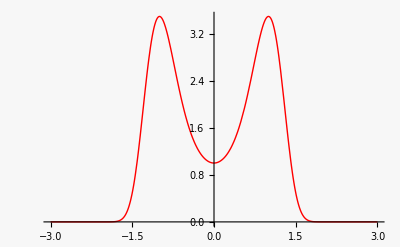

```mathematica
Plot[Exp[-1/Subscript[D, 0](-x^2/2+x^4/4)],{x,-xmax,xmax},PlotStyle->{Red,Thick}]  (* Boltzmann solution for equilibrium *)
```

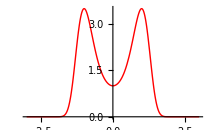

-Graphics-

data export

```mathematica
ueval[[1]]
```

InterpolatingFunction[…][t,x]

```mathematica
ueval[[1]]/.t->{0,1,2}/.x->{-2,0,2}
```

{{0.00108914,0.439391,0.0594651},{6.60398×10^-6,0.215807,0.00188625},{5.12466×10^-6,0.175931,0.000701351}}

```mathematica
pvals=100; qvals=100;  (* for exporting a matrix of values *)
dat=Table[ueval[[1]]/.t->((p-1)/(pvals-1)tmax)/.x->(-xmax+(q-1)/(qvals-1)2xmax),{q,qvals},{p,pvals}];
```

```mathematica
(* 
SetDirectory[NotebookDirectory[]];Export["fpeDoubleWell_out.dat", dat];
*)
```